Solve for a hit

```mathematica
Solve[Sqrt[r2+2*dot*t+v2*t^2]-vp*t==0,t]
```

{{t→(-dot-√(dot^2-r2 v2+r2 vp^2))/(v2-vp^2)},{t→(-dot+√(dot^2-r2 v2+r2 vp^2))/(v2-vp^2)}}

Special case for when projectile and target velocities are equal (singularity for expression above)

```mathematica
Solve[Sqrt[r2+2*dot*t+v*v*t^2]-v*t==0,t]
```

{{t→-r2/(2 dot)}}

Best effort closest approach

```mathematica
D[Sqrt[r2+2*dot*t+v2*t^2]-vp*t,t]//Simplify
```

(dot+t v2)/(√(r2+t (2 dot+t v2)))-vp

```mathematica
Assuming[v2>vp^2&&vp>0,Solve[(dot+t v2)/(√(r2+t (2 dot+t v2)))-vp==0,t]//Simplify]
```

{{t→(dot (-v2+vp^2)-vp √((dot^2-r2 v2) (-v2+vp^2)))/(v2 (v2-vp^2))},{t→(dot (-v2+vp^2)+vp √((dot^2-r2 v2) (-v2+vp^2)))/(v2 (v2-vp^2))}}

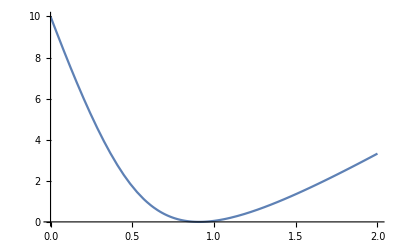

```mathematica
Plot[Sqrt[100-220t+221t^2]-10t,{t,0,2}]
```

```mathematica
D[Sqrt[100-220*t+221*t^2]-10*t,t]//Simplify
```

-10+(-110+221 t)/(√(100-220 t+221 t^2))

```mathematica
Solve[-10+(-110+221 t)/(√(100-220 t+221 t^2))==0,t]
```

{{t→10/11}}

```mathematica
{{t->(dot (-v2+vp^2)-vp √((dot^2-r2 v2) (-v2+vp^2)))/(v2 (v2-vp^2))},{t->(dot (-v2+vp^2)+vp √((dot^2-r2 v2) (-v2+vp^2)))/(v2 (v2-vp^2))}}/.{r2->100,v2->221,vp->10,dot->-110}
```

{{t→210/2431},{t→10/11}}

```mathematica
(-110+221 t)/(√(100-220 t+221 t^2))/.{t->210/2431}
```

-10